## Bezier-en kurbak

### Polinomioen bektore-espazioa

Polinomioak x aldagaiaren berreturen konbinazio lineal finituak dira, hau da,
	P(x)=a_k x^k+a_(k-1)x^(k-1)+a_(k-2)x^(k-2)+⋯+a_1 x+a_0 

P(x) polinomioaren maila k da.

Polinomioa deribatuz gero, P’(x) lortuko dugu, eta bere maila k-1 izango da.

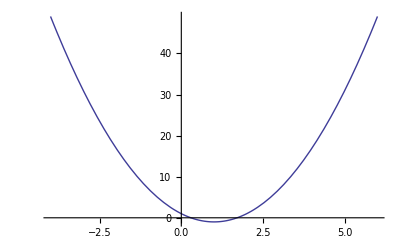

```mathematica
Plot[2x^2 -4x +1,{x,-4,6}]
```

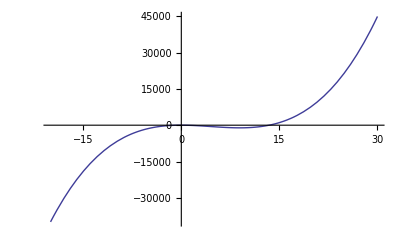

```mathematica
Plot[3x^3-40x^2 -4x +1,{x,-20,30}]
```

Maila bereko polinomioen multzoa bektore-espazio bat da. Bektore-espazioek oinarriak dituzte, horregatik polinomio bat oinarriko beste polinomio batzuen konbinazio gisa adieraz daiteke. Esate baterako, bektore-espazio horren oinarri kanonikoa honako polinomio sinple hauek osatzen dute:
				P_0=x^0;
P_1=x^1;
P_2=x^2;
… 
Polinomio horietan oinarrituz, beste edozein polinomio horien konbinazio lineal gisa adieraz daiteke:
		P(x)=a_k P_k+a_(k-1)P_(k-1)+a_(k-2)P_(k-2)+⋯+a_1 P_1+a_0 P_0.

Hemen, hiru mailako polinomioak erabiliko ditugu. Beraz, oinarrian lau polinomio izango ditugu.

```mathematica
p0[x_]:=1;
p1[x_]:= x;
p2[x_]:= x^2;
p3[x_]:= x^3;
polia[x_]:=2p2[x] -4p1[x] +1;
polib[x_]:= 3p3[x]-40p2[x] -4p1[x] +1;
```

```mathematica
Plot[polia[x],{x,-4,6}]
```

-Graphics-

```mathematica
Plot[polib[x],{x,-20,30}]
```

-Graphics-

### Bernstein-en oinarria

Orokorrean, [a,b] tartean definitzen diren polinomioak dira; baina, guk [0,1] tartean definitutakoak erabiliko ditugu. Polinomio hauek n mailako polinomioak dira; beraz, oinarrian n+1 polinomio behar dira. Polinomio hauen definizioa [0,1] tarterako honakoa da:
			B_i(x)=(n
i)(x^i(1-x))^(n-i),
non (n
i) zenbaki konbinatorioa baita.
Tartea (0,1) bada eta 3 mailako polinomioak nahi baditugu, hauek dira oinarriko lau polinomioak:
			B_0(x)=(3
0)(x^0(1-x))^3=(1-x)^3;
B_1(x)=(3
1)(x^1(1-x))^2=3(x(1-x))^2;
B_2(x)=(3
2)(x^2(1-x))^1=3x^2(1-x);
B_3(x)=(3
3)(x^3(1-x))^0=x^3.

```mathematica
b0[x_]:=(1-x)^3;
b1[x_]:= 3 x (1-x)^2;
b2[x_]:=  3 x^2 (1-x);
b3[x_]:= x^3 ;
```

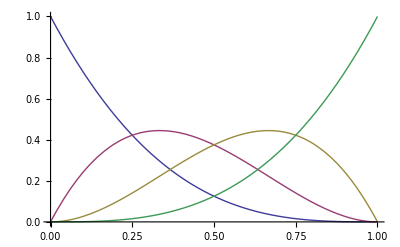

```mathematica
Plot[{b0[x], b1[x],b2[x],b3[x]},{x,0,1}]
```

1) Zenbat balio du puntu jakin batean lau polinomioen baturak? Egin itzazu proba batzuk.

```mathematica
b0[0.2]+b1[0.2]+b2[0.2]+b3[0.2]
```

1.

```mathematica
b0[0.4]+b1[0.4]+b2[0.4]+b3[0.4]
```

1.

```mathematica
b0[0.11]+b1[0.11]+b2[0.11]+b3[0.11]
```

1.

2) Zer emaitza orokor ondoriozta liteke? Egiazta ezazu.

Lau polinomioen batura putu jakin batean, beti 1 emaitza ematen du.

```mathematica
b0[x]+b1[x]+b2[x]+b3[x]
```

(1-x)^3+3 (1-x)^2 x+3 (1-x) x^2+x^3

```mathematica
Simplify[%14]
```

1

## Bezier-en polinomioa

Bila ezazu Wikipedian Bezier-en kurbaren definizioa eta ikus ezazu grafikoetan duen garrantzia.

3 mailako Bezier-en polinomioa Bernstein-en 3 mailako polinomioen konbinazio lineala da. Honela definituko dugu Bezier-en polinomioa:

```mathematica
bp[x_,a0_,a1_,a2_,a3_]:=a0 b0[x] + a1 b1[x] +a2 b2[x] + a3 b3[x];
```

0.3 (1-x)^3+3.6 (1-x)^2 x-3. (1-x) x^2+1. x^3

0.3+2.7 x-9.3 x^2+7.3 x^3

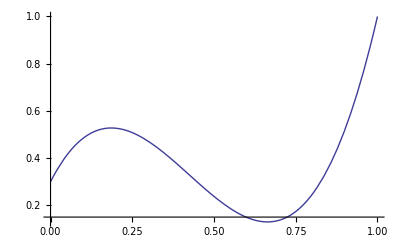

```mathematica
a0=0.3;
a1=1.2;
a2=-1.;
a3=1.;
bp[x,a0,a1,a2,a3]
Simplify[bp[x,a0,a1,a2,a3]]
Plot[bp[x,a0,a1,a2,a3],{x,0,1}]
```

3) Alda itzazu konbinazio linealaren koefizienteak eta lor itzazu Bezier-en polinomio batzuk. Zer ezaugarri komun dituzte Bezier-en polinomioek?

Ikusten da a0 (lehengo koefizientea) hasierako puntua dela, bertatik hasten dela funtzioa eta a3 (azkeneko koefizientea) non amaitzen den adierazten du. Gainera, polinomio ahuek jarraiak eta deribagarriak dira guztiak.

2 (1-x)^3-9 (1-x)^2 x+3.9 (1-x) x^2-7. x^3

2.-15. x+27.9 x^2-21.9 x^3

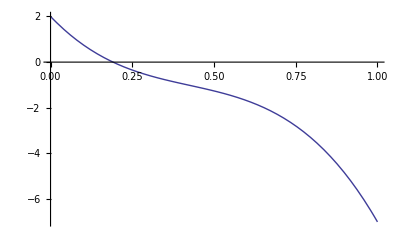

```mathematica
a0=2;
a1=-3;
a2=1.3;
a3=-7.;
bp[x,a0,a1,a2,a3]
Simplify[bp[x,a0,a1,a2,a3]]
Plot[bp[x,a0,a1,a2,a3],{x,0,1}]
```

-4 (1-x)^3-6 (1-x)^2 x+4.5 (1-x) x^2+9 x^3

-4.+6. x+4.5 x^2+2.5 x^3

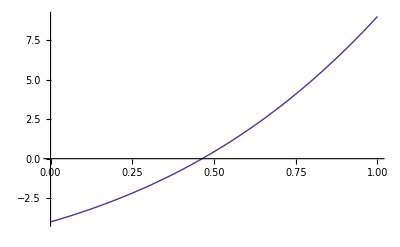

```mathematica
a0=-4;
a1=-2;
a2=1.5;
a3=9;
bp[x,a0,a1,a2,a3]
Simplify[bp[x,a0,a1,a2,a3]]
Plot[bp[x,a0,a1,a2,a3],{x,0,1}]
```

5 (1-x)^3-9 (1-x)^2 x+0.6 (1-x) x^2-0.9 x^3

5.-24. x+33.6 x^2-15.5 x^3

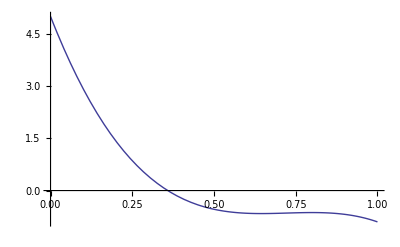

```mathematica
a0=5;
a1=-3;
a2=0.2;
a3=-0.9;
bp[x,a0,a1,a2,a3]
Simplify[bp[x,a0,a1,a2,a3]]
Plot[bp[x,a0,a1,a2,a3],{x,0,1}]
```

Orain, Bezier-en polinomioa kalkulatzen lagunduko diguten lau puntu emango ditugu. Lau puntu horiek finkoa dute lehenengo koordenatua (x); izan ere, [0,1] tartea hiru zati berdinetan zatituko dugu, eta lehenengo koordenatuak 0, 1/3, 2/3 eta 1 izango dira. Puntuen y koordenatua, ordea, gure esku egongo da aukeratzea.

1. (1-x)^3-60. (1-x)^2 x+51. (1-x) x^2+30. x^3

-63. (1-x)^2+222. (1-x) x+39. x^2

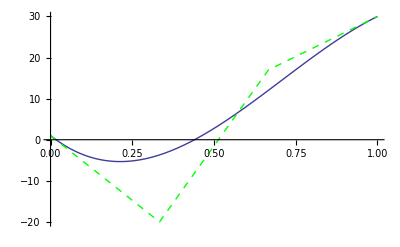

```mathematica
a0=1.;
a1=-20.;
a2=17.;
a3=30.;
max = Max[a0,a1,a2,a3];
min = Min[a0,a1,a2,a3];
bp[x,a0,a1,a2,a3]
D[bp[x,a0,a1,a2,a3],x]
kurba=Plot[bp[x,a0,a1,a2,a3],{x,0,1},PlotRange->{min,max}];
inguratzailea=ListPlot[{{0,a0},{1/3,a1},{2/3,a2},{1,a3}},Joined->True,PlotStyle->{Dashed,Green}];
Show[kurba,inguratzailea]
```

4) Zergatik aukeratzen ditugu LAU kontrol-puntu Bezier-en polinomioa kalkulatzeko?

Lau kontrol - puntu dira 3. mailako polinomioa delako.

5) Alda itzazu y koordenatuen balioak eta lor itzazu Bezier-en kurba batzuk eta dagozkien inguratzaileak. Zer ezaugarri komun berri dituzte?

kurbaren malda eta zuzenaren (inguratzailearen) malda berdinak direla hasierako eta amaierako puntuetan, bertan ukitzaileak direlako.

-24. (1-x)^3+156. (1-x)^2 x+132. (1-x) x^2-66. x^3

228. (1-x)^2-48. (1-x) x-330. x^2

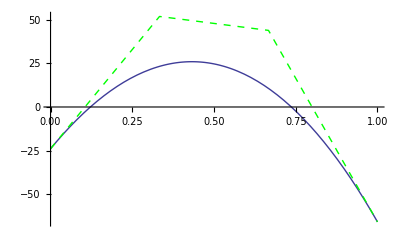

```mathematica
a0=-24.;
a1=52.;
a2=44.;
a3=-66.;
max = Max[a0,a1,a2,a3];
min = Min[a0,a1,a2,a3];
bp[x,a0,a1,a2,a3]
D[bp[x,a0,a1,a2,a3],x]
kurba=Plot[bp[x,a0,a1,a2,a3],{x,0,1},PlotRange->{min,max}];
inguratzailea=ListPlot[{{0,a0},{1/3,a1},{2/3,a2},{1,a3}},Joined->True,PlotStyle->{Dashed,Green}];
Show[kurba,inguratzailea]
```

31 (1-x)^3-69 (1-x)^2 x-165 (1-x) x^2+21. x^3

-162 (1-x)^2-192 (1-x) x+228. x^2

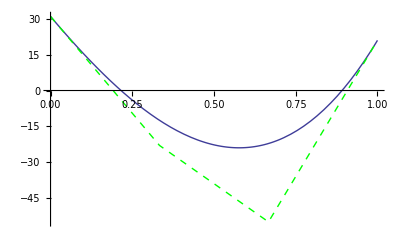

```mathematica
a0=31;
a1=-23;
a2=-55;
a3=21.;
max = Max[a0,a1,a2,a3];
min = Min[a0,a1,a2,a3];
bp[x,a0,a1,a2,a3]
D[bp[x,a0,a1,a2,a3],x]
kurba=Plot[bp[x,a0,a1,a2,a3],{x,0,1},PlotRange->{min,max}];
inguratzailea=ListPlot[{{0,a0},{1/3,a1},{2/3,a2},{1,a3}},Joined->True,PlotStyle->{Dashed,Green}];
Show[kurba,inguratzailea]
```

6) Bezier-en kurba zuzena izan al daiteke? Nola lor daiteke?

Bai, a1 a2 eta a3 puntuak lerro zuzenean, daudenean ahuen arteko maldak berdinak badira.

3 (1-x)^3+12 (1-x)^2 x+15 (1-x) x^2+6 x^3

3 (1-x)^2+6 (1-x) x+3 x^2

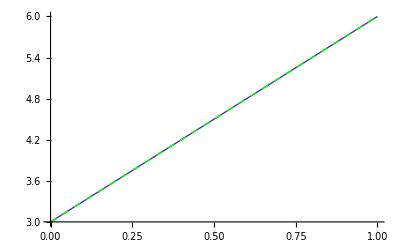

```mathematica
a0=3;
a1=4;
a2=5;
a3=6;
max = Max[a0,a1,a2,a3];
min = Min[a0,a1,a2,a3];
bp[x,a0,a1,a2,a3]
D[bp[x,a0,a1,a2,a3],x]
kurba=Plot[bp[x,a0,a1,a2,a3],{x,0,1},PlotRange->{min,max}];
inguratzailea=ListPlot[{{0,a0},{1/3,a1},{2/3,a2},{1,a3}},Joined->True,PlotStyle->{Dashed,Green}];
Show[kurba,inguratzailea]
```

7) Eta zuzen hori horizontala izan al daiteke? Nola lor daiteke? Zer erlazio dauka emaitza horrek bigarren galderaren erantzunarekin?

Bai, baldin eta inguratzailearen puntuak berdinak badira: y=konstantea.

3 (1-x)^3+9 (1-x)^2 x+9 (1-x) x^2+3 x^3

0

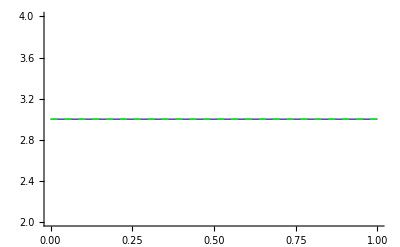

```mathematica
a0=3;
a1=3;
a2=3;
a3=3;
max = Max[a0,a1,a2,a3];
min = Min[a0,a1,a2,a3];
bp[x,a0,a1,a2,a3]
D[bp[x,a0,a1,a2,a3],x]
kurba=Plot[bp[x,a0,a1,a2,a3],{x,0,1},PlotRange->{min,max}];
inguratzailea=ListPlot[{{0,a0},{1/3,a1},{2/3,a2},{1,a3}},Joined->True,PlotStyle->{Dashed,Green}];
Show[kurba,inguratzailea]
```

Lehenengo irudira bueltatuko gara.

```mathematica
a0=1.;
a1=-20.;
a2=17.;
a3=30.;
max = Max[a0,a1,a2,a3];
min = Min[a0,a1,a2,a3];
bp[x,a0,a1,a2,a3]
D[bp[x,a0,a1,a2,a3],x]
kurba=Plot[bp[x,a0,a1,a2,a3],{x,0,1},PlotRange->{min,max}];
inguratzailea=ListPlot[{{0,a0},{1/3,a1},{2/3,a2},{1,a3}},Joined->True,PlotStyle->{Dashed,Green}];
Show[kurba,inguratzailea]
```

1. (1-x)^3-60. (1-x)^2 x+51. (1-x) x^2+30. x^3

-63. (1-x)^2+222. (1-x) x+39. x^2

-Graphics-

8) Zein da malda Bezier-en kurbaren hasieran eta bukaeran? Egiazta ezazu erantzuna kalkuluak eginez.

Inguratzailearen malda da a0 (hasierako puntua) eta a3 (bukaerako puntua) inguratzaileekin bat datoz, hasierako malda hasierako puntuaren deribatu izango da eta azkenekoa azkenekoaren deribatua. Hasierako puntua (0) eta bukaerakoan (1) ordezkatuz x ren lekuan.

```mathematica
-3. (1-0)^2+5. (1-0) 0+9. 0^2
```

```mathematica
-3.
```

Hori da bukaerako malda

```mathematica
-3. (1-1)^2+5. (1-1) 1+9. 1^2
```

9.

Hasierako malda

### Kurbaren ekuazio parametrikoak: x eta y koordenatuak t balioaren arabera

Orain, Bezier-en kurbaren ekuazio parametrikoak erabiliko ditugu. Kurba baten ekuazio parametrikoek kurbako puntuen koordenatuak parametro baten funtzioan ematen dituzte; hau da, (x,y) kurbako puntu bat bada, x = x(t) eta y = y(t) dira, eta parametroa t ∈ (a,b) ⊆ ℝ da. Gure kasuan, t ∈ (0,1) ⊆ ℝ izango da.

```mathematica
marraztukurba[puntulista_List]:= Module[{p0x,p0y,p1x,p1y,p2x,p2y,p3x,p3y,bpx,bpy,maxx,minx,maxy,miny,kurba,inguratzailea},
(p0x=puntulista[[1]][[1]];
p0y=puntulista[[1]][[2]];
p1x=puntulista[[2]][[1]];
p1y=puntulista[[2]][[2]];
p2x=puntulista[[3]][[1]];
p2y=puntulista[[3]][[2]];
p3x=puntulista[[4]][[1]];
p3y=puntulista[[4]][[2]];
bpx[t_]=bp[t,p0x,p1x,p2x,p3x];
bpy[t_]=bp[t,p0y,p1y,p2y,p3y];
maxx=Max[p0x,p1x,p2x,p3x];
maxy=Max[p0y,p1y,p2y,p3y];
minx=Min[p0x,p1x,p2x,p3x];
miny=Min[p0y,p1y,p2y,p3y];
kurba=ParametricPlot[{bpx[t],bpy[t]},{t,0,1},PlotRange->{{0.9minx,1.1maxx},{0.9miny,1.1maxy}}];
inguratzailea= ListPlot[{{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y}},Joined->True,PlotStyle->{Dashed,Green}];
Show[kurba,inguratzailea])];
kurbarenderibatuak[puntulista_List,pt_]:= Module[{p0x,p0y,p1x,p1y,p2x,p2y,p3x,p3y,bpx,bpy,t,xrena,yrena},
(p0x=puntulista[[1]][[1]];
p0y=puntulista[[1]][[2]];
p1x=puntulista[[2]][[1]];
p1y=puntulista[[2]][[2]];
p2x=puntulista[[3]][[1]];
p2y=puntulista[[3]][[2]];
p3x=puntulista[[4]][[1]];
p3y=puntulista[[4]][[2]];
bpx[t_]=bp[t,p0x,p1x,p2x,p3x];
bpy[t_]=bp[t,p0y,p1y,p2y,p3y];
{xrena,yrena}=D[{bpx[t],bpy[t]},t]/.t->pt;
{xrena,yrena, yrena/xrena})];
```

{{0.6868,0.5351},{0.368,0.4018},{0.5374,0.7527},{0.6413,0.1413}}

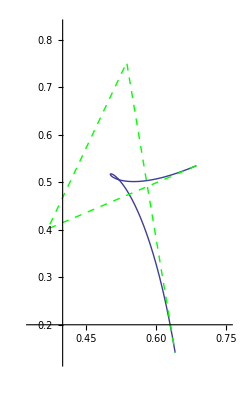

```mathematica
p1=Flatten[{{0.6868,0.5351}}];
p2=Flatten[{{0.368,0.4018}}];
p3=Flatten[{{0.5374,0.7527}}];
p4=Flatten[{{0.6413,0.1413}}];
puntuak={p1,p2,p3,p4}
marraztukurba[puntuak]
```

```mathematica
ta=0;
kurbarenderibatuak[puntuak,ta]
```

{-0.0999,0.89382,-8.94715}

9) Interpreta ezazu azkeneko aginduaren (kurbarenderibatuak) emaitza.

Kurbak deribagarriak eta jarraituak dira, gainera kontrol puntuak mugikorrak dira eta korapiloa dutenez ez dira funtzioak.

{{0.3456,0.5678},{0.312,0.865},{0.734,0.232},{0.24,2}}

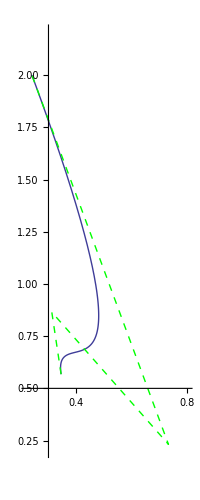

```mathematica
p1=Flatten[{{0.3456,0.5678}}];
p2=Flatten[{{0.312,0.865}}];
p3=Flatten[{{0.734,0.232}}];
p4=Flatten[{{0.24,2}}];
puntuak={p1,p2,p3,p4}
marraztukurba[puntuak]
```

Alda ezazu puntu bat zerrendan eta lor itzazu Bezier-en kurba batzuk eta dagozkien inguratzaileak.

Puntuak grafikoan bertan saguarekin aukeratzeko prozedura: aukeratu “graphics -> Drawing Tools -> ardatzak”; klik egin nahi duzun grafikoko puntuan; kontrol-C egin eta koordenatuak dagokien puntuan (p1, p2, p3 edo p4) itsatsi (kontrol-V). Puntu anitz ere kopia daitezke: klik, klik, klik eta klik egin nahi dituzun grafikoko puntuetan; kontrol-C egin eta lau puntuen koordenatuak “puntuak” eskuinean itsatsi (kontrol-V).

```mathematica
p1=Flatten[{{0.6868,0.5351}}];
p2=Flatten[{{0.368,0.4018}}];
p3=Flatten[{{0.5374,0.7527}}];
p4=Flatten[{{0.6413,0.1413}}];
puntuak={p1,p2,p3,p4}
marraztukurba[puntuak]
```

{{0.6868,0.5351},{0.368,0.4018},{0.5374,0.7527},{0.6413,0.1413}}

-Graphics-

```mathematica
ta=0;
kurbarenderibatuak[puntuak,ta]
```

{-0.9564,-0.3999,0.41813}

Alda ezazu puntuen zerrenda eta lor itzazu Bezier-en kurba batzuk eta dagozkien inguratzaileak.

Puntuak grafikoan bertan saguarekin aukeratzeko prozedura: aukeratu “graphics -> Drawing Tools -> ardatzak”; klik egin nahi duzun grafikoko puntuan; kontrol-C egin eta koordenatuak dagokien puntuan (p1, p2, p3 edo p4) itsatsi (kontrol-V). Puntu anitz ere kopia daitezke: klik, klik, klik eta klik egin nahi dituzun grafikoko puntuetan; kontrol-C egin eta lau puntuen koordenatuak “puntuak” eskuinean itsatsi (kontrol-V).

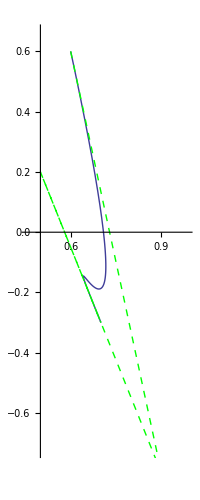

```mathematica
puntuak={{0.6,0.6},{0.9,-0.8},{0.5,0.2},{0.7,-0.3}};
marraztukurba[puntuak]
```

```mathematica
puntuak={{0.6,0.6},{0.9,-0.8},{0.5,0.2},{0.7,-0.3}};
marraztukurba[puntuak]
```

-Graphics-

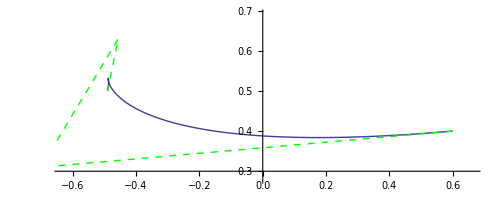

```mathematica
puntuak={{0.6,0.4},{-0.7,0.31},{-0.456,0.63},{-0.49,0.5}};
marraztukurba[puntuak]
```

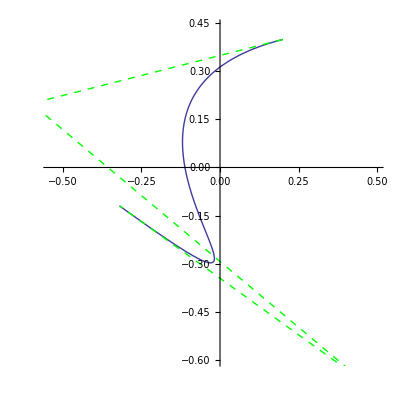

```mathematica
puntuak={{0.2,0.4},{-0.6,0.2},{0.453,-0.666},{-0.32,-0.12}};
marraztukurba[puntuak]
```

10) Zer ezaugarri komun dituzte, orain, Bezier-en kurbek?

Kurbaren hasiera eta bukaerak eta inguratzaileenak berdinak dira, eta orrez gain kontrol puntuak mugikorrak dira.

11) Zein da aurreko ataleko eta atal honetako Bezier-en kurben artean dagoen desberdintasuna?

Aurreko ataleko puntuak konstanteak direla, hauek, ordean, mugikorrak dira.

### Bezier-en kurbak "lotzen"

Orain, Bezier-en bi kurba erabiliko ditugu. Zer egin daiteke Bezier-en bi kurba lotzeko? Eta lotura hori leuna izatea nahi badugu, zer egin behar da?

Har ditzagun, lehendabizi, bi kurba:

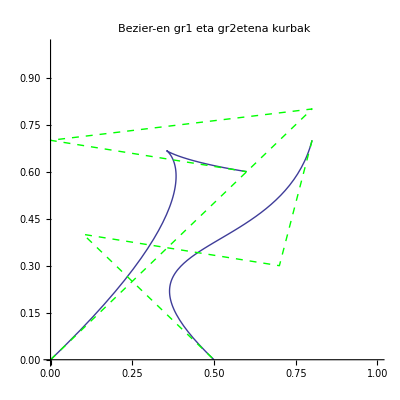

```mathematica
p0= {0,0};
p1= {0.8,0.8};
p2= {0,0.7};
p3= Flatten[{{0.6,0.6}}];
p4= {0.7,0.3};
p5={0.1,0.4};
p6={0.5,0};
p4ona={2p3[[1]]-p2[[1]],2p3[[2]]-p2[[2]]};
puntuak={p0,p1,p2,p3};
puntuak2={{0.8,0.7},p4,p5,p6};
puntuak3={p3,p4,p5,p6};
puntuak4={p3,2p3-p2,p5,p6};
gr1=marraztukurba[puntuak];
gr2etena=marraztukurba[puntuak2];
gr2jarraitua=marraztukurba[puntuak3];
gr2deribagarria=marraztukurba[puntuak4];
Show[gr1,gr2etena,PlotRange->{{0,1},{0,1}},PlotLabel->"Bezier-en gr1 eta gr2etena kurbak"]
```

12) Nola lor daiteke lotura jarritua izatea? Azal ezazu adibideko datuak erabiliz.

Lotura jarraitua kontrol puntuak lotuta lortuko ditugu. Hortarako kurba gutxikoa izan behar da.

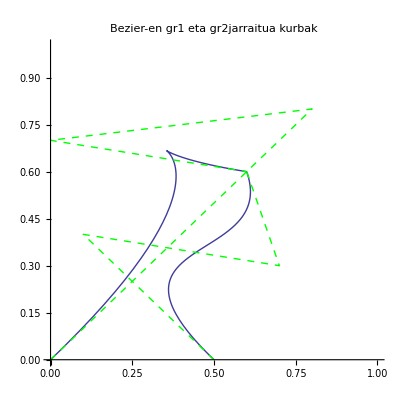

```mathematica
Show[gr1,gr2jarraitua,PlotRange->{{0,1},{0,1}},PlotLabel->"Bezier-en gr1 eta gr2jarraitua kurbak"]
```

13) Nola lor daiteke lotura leuna izatea? Azal ezazu adibideko datuak erabiliz.

Lotura leuna izan dadin bi kurben deribatuak berdinak izan behar dute.

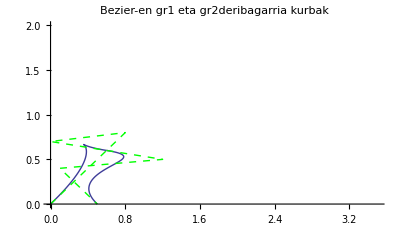

```mathematica
Show[gr1,gr2deribagarria,PlotRange->{{0,3.5},{0,2}},PlotLabel->"Bezier-en gr1 eta gr2deribagarria kurbak"]
```

14) Nola lortu dira p4ona puntuaren koordenatuak? Zer lortzen da koordenatu horiekin? Azal ezazu adibideko datuak erabiliz.

P4 ko koordenatuak lortzeko p4 = 2 p3 - p2 formula erabiltzen da, honek kontrol puntuak lerrokatuak egotea eragiten du.  p4=1,5 p3=0 p2=1,5 formulan ordezten: 1,5= 2 x 0 - 1,5 eta honen emaitza 1,5=1,5.

15) Kalkula itzazu deribatuak lehenengo kurbaren bukaeran (gr1 kurbaren bukaeran) eta jarraitutasuna bermatzen duten beste bi kurben hasieran (gr2jarraitua eta gr2deribagarria).

```mathematica
kurbarenderibatuak[puntuak,1]
```

{1.8,-0.3,-0.166667}

```mathematica
kurbarenderibatuak[puntuak3,0]
```

{0.3,-0.9,-3.}

```mathematica
kurbarenderibatuak[puntuak4,0]
```

{1.8,-0.3,-0.166667}

16) Kalkula itzazu deribatuak, beste bide batetik, lehenengo kurbaren bukaeran (gr1 kurbaren bukaeran) eta jarraitutasuna bermatzen duten beste bi kurben hasieran (gr2jarraitua eta gr2deribagarria). Egiazta ezazu balio berak ateratzen direla.

### Bukaerakoa

Bezier-en kurbak era errekurtsiboan marraz daitezke. Ondoko programak hori egiten du; lau puntu hartzen ditu abiapuntu gisa; ondoren, kurbako 100 puntu irudikatzen ditu.

```mathematica
puntualortu[puntulista_List,t_]:=
 Module[{marrakop,tartekopuntuak},
(marrakop=Length[puntulista];
For[i=1;tartekopuntuak={},i<marrakop,i++,
tartekopuntuak = Append[tartekopuntuak, puntulista[[i]]+t (puntulista[[i+1]]-puntulista[[i]])]];
If[Equal[marrakop,2],tartekopuntuak[[1]],puntualortu[tartekopuntuak,t]])
];
kurbakopuntuaklortu[puntulista_List,puntukop_]:= Module[{puntuak,t},
(puntuak ={};
gehikuntza = 1./(puntukop-1.);
For[t=0,t<1,t=t+gehikuntza,
    puntuak=Append[puntuak,puntualortu[puntulista,t]]
    ];
puntuak=Append[puntuak,puntulista[[-1]]];
puntuak)
];
```

```mathematica
kontrolekoak={{0.04159,0.139},{0.03871,0.4743},{0.4123,0.3404},{0.5674,0.1363}};

puntubak=kurbakopuntuaklortu[kontrolekoak,100];
```

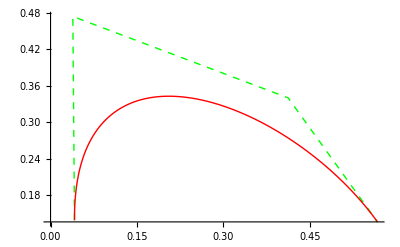

```mathematica
gr1=ListPlot[kontrolekoak,Joined->True,PlotStyle->{Dashed,Green}];
gr2=ListPlot[puntubak,Joined->True,PlotStyle->{Red}];
Show[gr1,gr2]
```